# Add track overlay on cell image

```mathematica
analysisFolder ="/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/Analysis/";
trackfile = analysisFolder <> "MAX_TA50-1_myTrack_red_1_myTrack_red.dat";
```

For the STATIC movie:

```mathematica
(*FOR SINGLE-FRAME MOVIE:  *)
imgfile = "/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/MAX_TA50-1.tif";
thred =<<(analysisFolder<>"MAX_TA50-1_thred.dat" )
thgrn =<<(analysisFolder<>"MAX_TA50-1_thgreen.dat" )
thblu =<<(analysisFolder<>"MAX_TA50-1_thblue.dat" )
```

{0.004,0.034}

{0.004,0.074}

{0.004,0.052}

```mathematica
(*For single frame image*) myColMovie=Import[imgfile] ;
Dimensions@myColMovie
```

For the TIME SERIES movie:

```mathematica
(*FOR MOVIE OVER TIME *)
imgfile = "/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/MAX_TA50-1.tif";
thred =<<(analysisFolder<>"MAX_TA50-1_thred.dat" )
thgrn =<<(analysisFolder<>"MAX_TA50-1_thgreen.dat" )
thblu =<<(analysisFolder<>"MAX_TA50-1_thblue.dat" )
(*For MultiFrame image*) 
myColMovie=Import[imgfile]//Partition[#,3]&//Transpose;
Dimensions@myColMovie
```

{0.004,0.034}

{0.004,0.074}

{0.004,0.052}

{3,54}

```mathematica
(*FOR MULTI-FRMAE IMAGE OVER TIME:  *)
frame = -10;
imgFrame =  Table[ 
ImageAdjust[ myColMovie[[ch, frame]], {{.6,.7,1.25},{.5,.5,1.5},{0,.7,1.5}}[[ch]],{thred,thgrn,thblu}[[ch]]  ],{ch,1,3}]//ColorCombine
```

-Graphics-

```mathematica
(*FOR ONE FRMAE STILL IAMGE: *)
imgFrame =  Table[ 
ImageAdjust[ myColMovie[[ch]], {{.35,0,3},{1,.25,.9},{.8,1,1.8}}[[ch]],{thred,thgrn,thblu}[[ch]]  ],{ch,1,3}]//ColorCombine
```

-Graphics-

```mathematica
track = Get@trackfile;
locs = track[[1,1,All,3,1]]
frames  = track[[1,1,All,2]]
```

Integer[]

Integer[]

```mathematica
Graphics[{Yellow,Thick,  Line[locs] }];
```

```mathematica
(* ColorCombine[ImageAdjust/@ myColMovie[[All,frame]] ]
```

```mathematica
locs[[frame;;]]//Length
```

10

```mathematica
(*For locations STARTING at the beginning 
ops = Table[ n,{n,0,1, 1/Length@locs[[frame;;]] }]

For locations ENDING AT the end of track *)
ops = Table[ n,{n,0,1, 1/Length@locs[[1;;frame]] }]
```

{0,1/45,2/45,1/15,4/45,1/9,2/15,7/45,8/45,1/5,2/9,11/45,4/15,13/45,14/45,1/3,16/45,17/45,2/5,19/45,4/9,7/15,22/45,23/45,8/15,5/9,26/45,3/5,28/45,29/45,2/3,31/45,32/45,11/15,34/45,7/9,4/5,37/45,38/45,13/15,8/9,41/45,14/15,43/45,44/45,1}

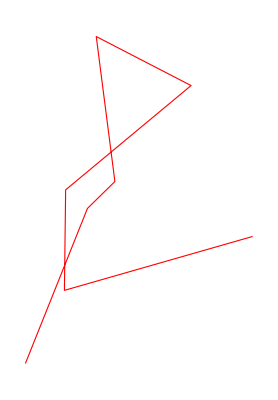

```mathematica
Graphics[{ RGBColor[1, 0, 0],Thickness->.002,  Line[locs[[frame;; (*Change what frames to draw your track, here*)]]    ] }]
```

```mathematica
(*FOR image STARTING AT track  : 
Show[imgFrame , Graphics[{ Yellow,Thickness->.002,  Line[locs[[frame;; (*Change what frames to draw your track, here*)]]  ] }]  ]
```

```mathematica
Show[imgFrame , Graphics[{ Yellow,Thickness->.002,  Line[locs[[1 ;; frame (*Change what frames to draw your track, here*)]]  ] }]  ]
```

-Graphics-

```mathematica
trackMovie  = Show[imgFrame , Graphics[{Opacity[0.4,Yellow],Thickness->.002,  Line[locs[[1;;frame (*Change what frames to draw your track, here*)]] ] }]  ]
```

-Graphics-

```mathematica
Export[(StringTake[ trackfile , {1,-5}] <> "_RGBt_registered.tif") , trackMovie   ]
```

/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190508_TA05/Analysis/MAX_TA05_RGBonly_myTrack_red_2_myTrack_red_RGBt_registered.tif

## Tracking R, G, and B:

```mathematica
analysisFolder
```

/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/Analysis/MAX_TA50-1

```mathematica
trackfileB ="/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/Analysis/MAX_TA50-1_myTrack_blue_1.dat";
trackfileR ="/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/Analysis/MAX_TA50-1_myTrack_red_19.dat";
trackfileG = "/Users/ccialek/OneDrive - Colostate/_Argonaute paper/Figures/Figure 2 and S2/Data and code/_90m tracking/_All_Tracks_used_in_figure/_20190611_TA50/Analysis/MAX_TA50-1_myTrack_green_1.dat";
trackR = Get@trackfileR;
trackG = Get@trackfileG;
trackB= Get@trackfileB;
```

```mathematica
(*Manipulate[myColMovie⟦ch, frame⟧//ImageAdjust[#,{0,0,1},{thred,thgrn,thblu}[[ch]]] &,
{ch,1,3,1, RadioButton}, {frame,1,Length@myColMovie[[1]],1}]
```

```mathematica
locsR
```

{{140.324,308.491},{118.739,301.76},{138.631,285.746},{148.859,299.648},{139.663,303.323},{147.945,301.484},{151.153,315.815},{159.584,314.377},{164.521,308.979},{168.888,310.507},{169.351,313.445},{174.378,309.086},{172.898,310.22},{175.939,307.86},{176.576,312.839},{189.948,301.376},{193.155,307.774},{184.332,311.646},{186.288,302.45},{182.878,300.715},{182.26,295.575},{182.466,297.704},{184.082,299.662},{183.602,299.794},{182.66,296.884},{184.978,297.004},{188.875,297.873},{191.481,299.213},{189.29,298.927},{195.02,298.89},{199.734,299.874},{201.618,298.437},{199.614,299.975},{196.497,297.464},{195.044,295.777},{193.218,297.294},{195.194,296.559},{194.438,296.706},{195.364,298.241},{193.148,296.853},{194.587,297.423},{196.593,299.649},{196.301,298.07},{196.009,296.49},{197.37,297.851},{198.359,300.318},{199.348,302.784},{200.222,303.64},{199.628,308.254},{199.303,306.628},{198.978,305.001},{198.653,303.375},{198.614,300.177},{204.612,301.892}}

```mathematica
locsB = {{140.56640384932473,307.1012171540779},{117.31334600932591,300.6732423378152},{137.04208617699393,284.7502421334775},{150.0465115232265,300.6420507742168},{139.10338176352707,302.3013026052104},{146.83129703408588,301.56647349993966},{150.93511127342714,313.15356544523866},{159.5840941236981,313.3769876987699},{164.42072619012873,306.86902016870494},{167.94930819823585,309.56847627636876},{168.0518195797027,311.2331710234068},{173.89784723269491,309.6461318051576},{172.33683613165826,309.3340769441509},{176.480677979733,306.840015280682},{176.19431522939777,310.3563483049925},{188.40601913321757,301.18886392265006},{192.65761235324908,306.3324422343528},{184.78886584972042,311.9517225555348},{185.52736185041934,300.9983150155095},{182.62508284521826,299.1401382843427},{181.1425581188207,294.5700632404026},{182.15243253699583,296.7469049231067},{182.94521439297034,298.5285968522329},{184.0686265428525,298.06487506657714},{182.5121034970348,296.11377498258867},{179.8343142255529,293.91243248191887},{189.8686173860637,298.51866726241195},{191.7052040673321,297.07755492922655},{189.40280252394498,297.1114168151437},{196.8559945168887,296.18006045481707},{198.83559470770894,298.3430201161064},{199.29518155341478,297.2611801402795},{198.82709321352303,298.05328137855804},{195.32962314034071,296.3107254040017},{192.3623146423561,296.0175410456158},{194.46365658756346,294.8465725309145},{197.39009330406148,300.39306622758875},{195.56823379490038,296.63354344684774},{194.5530570613679,296.2768921292711},{192.57574577999867,296.01935738900056},{193.3096067948024,296.04566526800215},{193.83843241827574,297.95297731006406},{197.00608667525083,293.1284733237539},{199.8222751241489,311.58518916705066},{200.2567019688904,298.0664610252277},{196.19525472198274,302.01378170971384},{198.72546217636403,299.85564794707057},{194.46849457331805,300.1754322243208},{199.45928231657862,306.85184901028083},{191.24664939855967,308.3313612370244},{192.89347828226656,307.40286321715763},{197.65481546660467,302.645866883602},{211.79015092435432,294.25375017202623},{204.38440330594898,301.2151407010892}}   ;
```

```mathematica
frame=31;
locsR = trackR[[All,3,1]];
locsG = trackG[[ All,3,1]];
locsB = trackB[[ All,3,1]];
frames  = track[[ All,2]];
```

```mathematica
94.7*31/60
```

48.9283

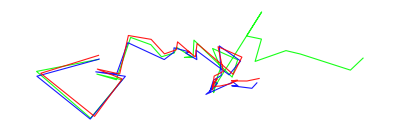

```mathematica
mytrack3col = Show[ 
Graphics[{ Opacity[ 0.9,Green], Thickness->.002,  Line[locsG[[1;;frame]]    ] }]  , 
Graphics[{Opacity[ 0.9,Blue],Thickness->.002,  Line[locsB[[1;;frame]]    ] }]  ,
Graphics[{Opacity[ 0.9, RGBColor[1, 0, 0]],Thickness->.002,  Line[locsR[[1;;frame]]    ] }]  ]
```

```mathematica
locsScale = Transpose[{ {512-20, (512-20)-76.9 } , {20,20}  } ] ; 
scalebar = Graphics[{Opacity[ 0.9,White],Thickness->.002,  Line[locsScale  ] }]   ;
```

```mathematica
imgFrame =  Table[ 
ImageAdjust[ myColMovie[[ch, frame]], {{.6,.7,1.25},{.5,.5,1.5},{0,.7,1.5}}[[ch]],{thred,thgrn,thblu}[[ch]]  ],{ch,1,3}]//ColorCombine ;
```

```mathematica
trackMovie  = Show[imgFrame ,  
mytrack3col , scalebar ]
```

-Graphics-